Quantum Fourier Transform: Semiclassical Implementation

Demonstrationpaclet:QuantumMob/Q3/tutorial/QuantumFourierTransformSemiclassical#2119699967 | Testspaclet:QuantumMob/Q3/tutorial/QuantumFourierTransformSemiclassical#1221384869

It is widely believed that the quantum entanglement is essential for quantum speed-up of quantum computation [1] or the precision measurement beyond the quantum standard limit (also known as the Heisenberg limit) [2]. The semiclassical implementation, to be demonstrated below, of the quantum Fourier transform (QFT) suggests that it is not necessarily the case.  In the semiclassical scheme, the single-qubit measurements and subsequent single-qubit gates controlled by the measurement results (classical signals) are sufficient to perform the QFT efficiently.

Demonstration

First, load the package.

```mathematica
Needs["QuantumMob`Q3`"]
```

Choose the symbol S to represent qubits.

```mathematica
Let[Qubit,S]
```

```mathematica
$n=5;
ss=S[Range[$n],None]
```

{S_1,S_2,S_3,S_4,S_5}

Here are some handy functions to be used in the circuit implementations.

```mathematica
CP[j_,j_]:=S[j,6]
CP[j_,k_]:=ControlledGate[S[j],S[k,C[k-j-1]],"Label"->Subscript["S",j-k]]/;j>k
CP[j_,k_]:=ControlledGate[S[j],S[k,C[j-k-1]],"Label"->Subscript["S",k-j]]/;j<k
SW[j_]:=SWAP[S[j],S[$n-j+1]]
```

This is the typical QFT circuit explained in most textbooks.

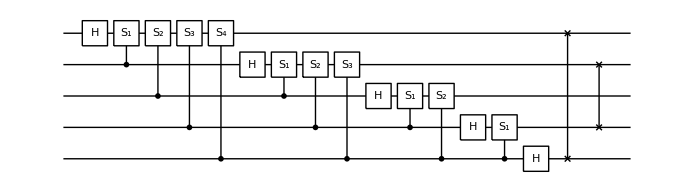

```mathematica
swaps=Table[SW[j],{j,1,$n/2}];
gates4a=Catenate@Table[CP[j,k],{k,1,$n},{j,k,$n}];
qft4a=Join[gates4a,swaps];
qc4a=QuantumCircuit[Sequence@@qft4a]
```

You can convince yourself that this circuit is equivalent to the above.

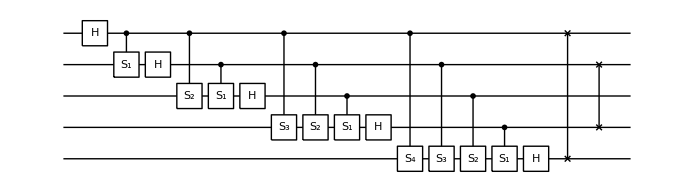

```mathematica
swaps=Table[SW[j],{j,1,$n/2}];
gates4b=Catenate@Table[CP[j,k],{k,1,$n},{j,1,k}];
qft4b=Join[gates4b,swaps];
qc4b=QuantumCircuit[Sequence@@qft4b]
```

Now consider measurements at the end of the calculation.

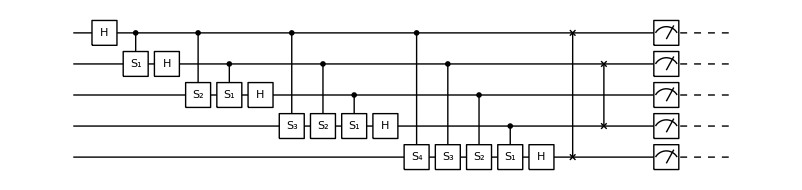

```mathematica
qft4c=Join[gates4b,swaps,{"Spacer",Measurement[Through[ss[3]]],"Spacer"}];
qc4c=QuantumCircuit[Sequence@@qft4c]
```

The measurements and SWAP gates can be exchanged. The resulting circuit is equivalent to the semiclassical implementation of the QFT as discussed in Ref. [1].

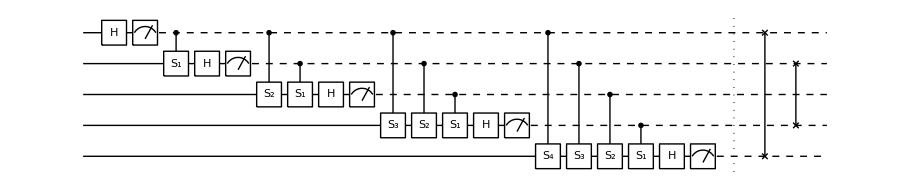

```mathematica
mm=Measurement/@Through[ss[3]];
mm=Transpose@{mm};
gates4d=Table[CP[j,k],{k,1,$n},{j,1,k}];
more=Catenate[Join@@@Thread[{gates4d,mm}]];
qft4d=Join[more,{"Separator"},swaps];
qc4d=QuantumCircuit[Sequence@@qft4d]
```

Tests

```mathematica
mat4a=Matrix[qc4a];
mat4b=Matrix[qc4b];
mat4a-mat4b//N//Chop//Normal//Flatten
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Information Systems with Q3
▪QuantumCircuit Usage Examples
▪Quantum Fourier Transform
▪Quantum Teleportation

| Related Links
▪R. B. Griffiths and C.-S. Niu, Physical Review Letters 76 (17), 3228 (1996)https://doi.org/10.1103/physrevlett.76.3228, “Semiclassical Fourier Transform for Quantum Computation.”
▪J. Chiaverini https://doi.org/10.1126%2Fscience.1110335et al., Science 308 (5724), 997 (2005)https://doi.org/10.1126%2Fscience.1110335, “Implementation of the Semiclassical Quantum Fourier Transform in a Scalable System.”
▪B. L. Higgins, D. W. Berry, S. D. Bartlett, H. M. Wiseman, & G. J. Pryde, Nature 450 (7168), 393 (2007)https://doi.org/10.1038/nature06257, “Entanglement-free Heisenberg-limited phase estimation.”
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).

| Related Wolfram Education Group Courses
An Elementary Introduction to the Wolfram Languagehttps://www.wolfram.com/language/elementary-introduction/
The Wolfram Language: Fast Introduction for Programmershttps://www.wolfram.com/language/fast-introduction-for-programmers/